```mathematica
f[x_,t_]:=a t^2-Log[Cos[x+t]^2]
```

```mathematica
D[f[x,t],t,t]
```

2 a+2 Sec[t+x]^2

```mathematica
D[f[x,t],x]^2
```

4 Tan[t+x]^2

```mathematica
D[f[x,t],t,t]-D[f[x,t],x]^2//Simplify
```

2 (a+Sec[t+x]^2-2 Tan[t+x]^2)

```mathematica
Sec[t+x]^2//Simplify
```

Sec[t+x]^2

```mathematica
Sec[t+x]^2==1+Tan[t+x]^2//Simplify
```

True

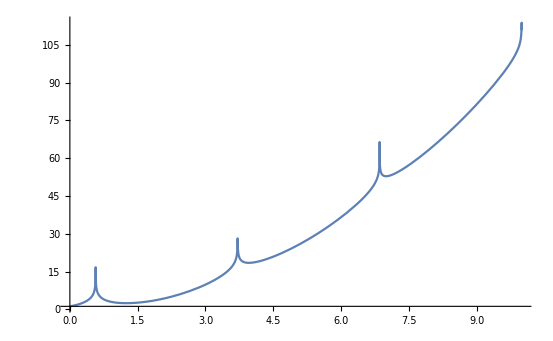

```mathematica
Plot[a t^2-Log[Cos[x+t]^2]/.{x->1,a->1},{t,0,10},PlotRange->Full]
```